### Reproduksi hasil Ho dan Matsuo

#### Hitung exterior

```mathematica
Clear["Global`*"];
α=5.* 10.^-2;
κ =1;
a0:=10.
rs00:=50000.
ρ00:=50000.
R=10./0.9999999998
rs0:=R+a0 Log[R/a0-1]
r0=rs00;
RR=x/.Solve[x+a0 Log[x/a0-1]==r0,x][[1]]
rn=-50.*10^3;
ν0=Log[1-a0/RR];
ν01=a0/RR^2;
ρ0[rs_]=0.;
P0[rs_]=0.;

pers1=-ν'[rs]+1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)));
(*Persamaan differensial metrik*)
pers2=-r''[rs]+1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ r[rs]^2 ρ0[rs]-4 r'[rs]^2+1/α 8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)))+1/α 4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)))^2-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) P0[rs] α κ-2 ⅇ^ν[rs] α κ ρ0[rs]) ν'[rs]-2 ⅇ^ν[rs] α κ ρ0'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)))));
```

10.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

49914.8

Compactnessnya melanggar Buchdahl limit

```mathematica
N[{κ ρ0[rs0],rs0,a0,α}]
```

{0.,-213.327,10.,0.05}

```mathematica
a0/x/.Solve[rs0==x+a0 Log[x/a0-1],x][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.

```mathematica
s=NDSolve[{pers1==0,pers2==0,ν[r0]==ν0,r[r0]==RR,r'[r0]==(1-a0/RR)},{ν,r},{rs,rs00,rs0}]
νo[rs_]=Evaluate[ν[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
```

{{ν→InterpolatingFunction[{{-213.327, 50000.}}, <>],r→InterpolatingFunction[{{-213.327, 50000.}}, <>]}}

```mathematica
rs0
a0/(1-Exp[νo[rs0]])
x/.Solve[rs0==x+a0 Log[x/a0-1],x][[1]]
ro[rs0]
```

-213.327

10.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

10.

10.0508

#### Hitung interior

```mathematica
ν0=νo[rs0];
ρ0[rs_]=ρ00/κ;
P0[rs_]=ρ0[rs] Exp[ν0/2];

pers1=-ν'[rs]+1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)));
(*Persamaan differensial metrik*)
pers2=-r''[rs]+1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ r[rs]^2 ρ0[rs]-4 r'[rs]^2+1/α 8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)))+1/α 4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)))^2-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) P0[rs] α κ-2 ⅇ^ν[rs] α κ ρ0[rs]) ν'[rs]-2 ⅇ^ν[rs] α κ ρ0'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) P0[rs] α κ-ⅇ^ν[rs] α κ ρ0[rs]+r'[rs]^2)))));
R=x/.Solve[rs0==x+a0 Log[x/a0-1],x][[1]];
r0=R+a0 Log[R/a0-1];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{ν[rs0]==ν0,r[rs0]==ro[rs0],r'[rs0]==ro'[rs0]}
```

{ν[-213.327]==-22.2749,r[-213.327]==10.0508,r'[-213.327]==-0.000124165}

```mathematica
s2=NDSolve[{pers1==0,pers2==0,ν[rs0]==ν0,r[rs0]==ro[rs0],r'[rs0]==ro'[rs0]},{ν,r},{rs,rs0,rn}]
νi[rs_]=Evaluate[ν[rs]/.s2][[1]];
ri[rs_]=Evaluate[r[rs]/.s2][[1]];
```

{{ν→InterpolatingFunction[{{-50000., -213.327}}, <>],r→InterpolatingFunction[{{-50000., -213.327}}, <>]}}

```mathematica
νsol[rs_]:=Piecewise[{{νo[rs],rs≥y},{νi[rs],rs<y}}]/.{y->rs0}
rsol[rs_]:=Piecewise[{{ro[rs],rs≥y},{ri[rs],rs<y}}]/.{y->rs0}
Psol[rs_]:=-ρ0[rs0]+P0[rs0]Exp[-νsol[rs]/2]
```

InterpolatingFunction::dmval: Input value {-49998.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

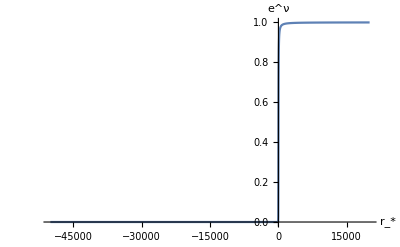

```mathematica
Plot[Exp[νsol[rs]],{rs,rn,20000},AxesLabel->{"r_*","e^ν"}]
```

InterpolatingFunction::dmval: Input value {-1499.96} lies outside the range of data in the interpolating function. Extrapolation will be used.

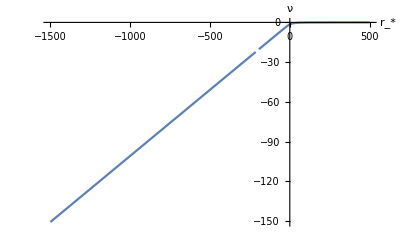

```mathematica
Plot[νsol[rs],{rs,-1500,500},AxesLabel->{"r_*","ν"},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-1499.96} lies outside the range of data in the interpolating function. Extrapolation will be used.

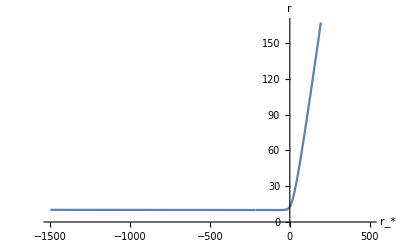

```mathematica
Plot[rsol[rs],{rs,-1500,500},AxesLabel->{"r_*","r"}]
```

InterpolatingFunction::dmval: Input value {-49.999} lies outside the range of data in the interpolating function. Extrapolation will be used.

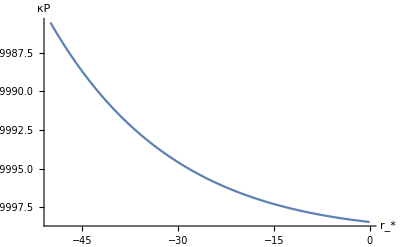

```mathematica
Plot[Psol[rs],{rs,-50,0},AxesLabel->{"r_*","κP"},PlotRange->All]
```

```mathematica
{νo[rs0],νi[rs0]}
{ro[rs0],ri[rs0]}
```

{-22.2749,-22.2749}

{10.0508,10.0508}

InterpolatingFunction::dmval: Input value {-1499.97} lies outside the range of data in the interpolating function. Extrapolation will be used.

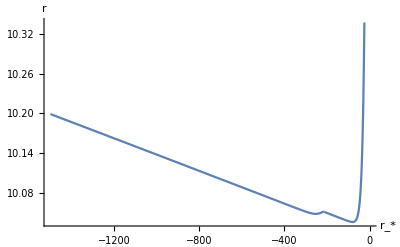

```mathematica
Plot[rsol[rs],{rs,-1500,0},AxesLabel->{"r_*","r"}]
```